```mathematica
sig[x_]:=1/(1+E^(-x))
```

```mathematica
nn[x_,θ_,f_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23},
{w11,w12,w13,w14,w21,w22,w23} = θ;
(* Return[f[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23]]; *)
Return[w21*f[w11*x+w12]+w22*f[w13*x+w14]+w23];
]
```

```mathematica
gradient[x_,weights_,fn_:Tanh]:=Module[{w11,w12,w13,w14,w21,w22,w23,w,d},
w={w11,w12,w13,w14,w21,w22,w23};
d=D[nn[x,w,fn],{w}]/.MapThread[#1->#2&,{w,weights}];
Return[d]
]
```

```mathematica
(*
Implement a simple backpropagation algorithm and print out the
weights along the way. Use this to really understand what is 
going on. And then use it as a way to generate data to test your
software with. Eg, you can generate the entire sequience of weights,
 outputs, and errors for 10, 100, or even 1000 iterations of 
backpropagation and use that to verify your python program.
*)
```

```mathematica
train[data_,init_,lr_:.1]:=Module[{θ,i,j,errors,adjust,batches},
θ=init;
batches=Table[
errors = Map[d↦{d[[1]],d[[2]]-nn[d[[1]],θ]},data];
adjust =Table[
θ +=gradient[e[[1]],θ]*e[[2]]*lr
,{e,errors}]
(*,{e,RandomSample[errors,10]}]*)
(* θ += Mean@adjust *)
,{5000}];
Return[batches]
]
```

```mathematica
data={{2,.9},{1,.3},{-1,.4},{-2,.1}};
data2=Table[{x,0.3-0.13333333333333347 x+0.05000000000000004 x^2+0.08333333333333337 x^3},{x,-2,2,.2}];
θ = {.4,-.2,.6,.1,.4,-.2,.6};
```

```mathematica
θs = train[data2, θ,.01];
```

{{-2.,0.192669},{-1.8,0.228063},{-1.6,0.265669},{-1.4,0.304111},{-1.2,0.341075},{-1.,0.37304},{-0.8,0.395229},{-0.6,0.402165},{-0.4,0.38935},{-0.2,0.356211},{0.,0.309072},{0.2,0.261353},{0.4,0.229194},{0.6,0.224878},{0.8,0.252932},{1.,0.310813},{1.2,0.392084},{1.4,0.48937},{1.6,0.596023},{1.8,0.706703},{2.,0.817382}}

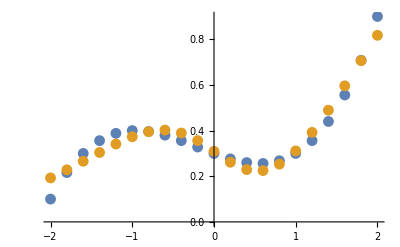

```mathematica
nnData =Map[in ↦{in, nn[in,θs[[-1,-1]]]},data2[[All,1]]]
ListPlot[{data2,nnData}]
```

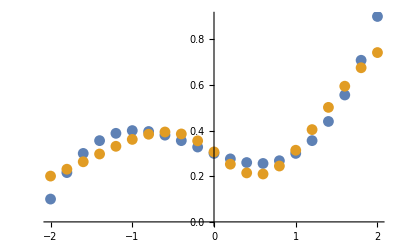

```mathematica
ListPlot[Flatten[θs,1]ᵀ]
```

-Graphics-

```mathematica
NonlinearModelFit[data,a+b*x+c*x^2+d*x^3,{a,b,c,d},x]
```

FittedModel[0.3-0.133333 x+0.05 x^2+0.0833333 x^3]